```mathematica
Plot3D[Im[ArcSin[(x+I y)^4]],{x,-2,2},{y,-2,2},Mesh->None,PlotStyle->Directive[Yellow,Specularity[White,20],Opacity[0.8]],ExclusionsStyle->{None,Red}]
```

-Graphics3D-

0.618方法

寻找单谷区间

```mathematica
Clear[mySingleInterval];
mySingleInterval[f_, step_:0.5] := Module[{x1, x2},
x1 = 0.0; x2 = step;
While[f[x1] > f[x2],
x1 = x2;
x2 = x2 + step;
];
Return[{0, x2}]
];
```

0.618方法

```mathematica
Clear[my0618];
my0618[f_, a1_, b1_, ϵ_:0.001, isTrace_:True] :=
Module[{tmp, a, b, w, t1, t2, f1, f2, loop, maxLoop, table},
a = a1; b = b1;
w = 0.618;
tmp= w(b - a);
t1 = b - tmp; t2 = a + tmp;
f1 = f[t1]; f2 = f[t2];
loop = 0;
table = {};
maxLoop= Floor[Log[w, ϵ/(b1 - a1)]] + 1;
While[loop ≤maxLoop,
If[isTrace,
AppendTo[table, {loop, a, b, t1, t2, f1, f2}];
];
loop = loop + 1;
If[f1 ≤ f2,
(*step4*)
If[t2 - a ≤ ϵ,
If[isTrace, Print[TableForm[table, TableHeadings->
{None, {"loop", "a", "b", "t1", "t2", "f1", "f2"}}]]
];
Return[TableForm[{{a, t2, t2 - a, t1}},
TableHeadings-> {None, {"a", "b", "b-a", "t*"}}]],
(*else*)
b = t2; t2 = t1; t1 = b - 0.618(b - a);
f2 = f1; f1 = f[t1];
],
If[b - t1 ≤ ϵ,
If[isTrace, Print[TableForm[table, TableHeadings->
{None, {"loop", "a", "b", "t1", "t2", "f1", "f2"}}]]
];
Return[TableForm[{{t1, b, b - t1, t2}},
TableHeadings-> {None, {"a", "b", "b-a", "t*"}}]],
a = t1; t1 = t2; t2 = a + 0.618(b - a);
f1 = f2; f2 = f[t2];
]
]
];
Print["loop=", loop];
];
```

测试

{0,0.817}

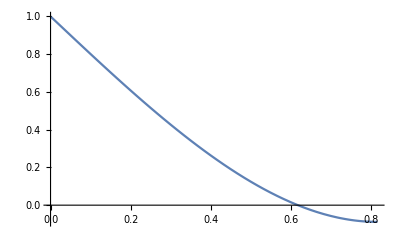

0 | 0 | 0.817 | 0.312094 | 0.504906 | 0.406211 | 0.118904
1 | 0.312094 | 0.817 | 0.504906 | 0.624126 | 0.118904 | -0.00513409
2 | 0.504906 | 0.817 | 0.624126 | 0.69778 | -0.00513409 | -0.0558131
3 | 0.624126 | 0.817 | 0.69778 | 0.743322 | -0.0558131 | -0.0759381
4 | 0.69778 | 0.817 | 0.743322 | 0.771458 | -0.0759381 | -0.0837847
5 | 0.743322 | 0.817 | 0.771458 | 0.788855 | -0.0837847 | -0.0868117

0.771458 | 0.817 | 0.045542 | 0.788855

```mathematica
Clear[f, t, a, b, r, ϵ];
f[t_] = t^3-2t+1;
{a, b} = mySingleInterval[f, step = 0.001]
Plot[f[t], {t, a, b}]
r=my0618[f,a,b,ϵ=0.05,isTrace=True]
```